## Notes

This program extracts Apple Health data (.csv format)  and graphs and analyzes heart rate data.

## Initial Importing and Formatting Data Code

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jofre/Documents/GitHub/Connie_Summer2018

```mathematica
heartRate= Import["HKQuantityTypeIdentifierHeartRate.csv","CSV"];
```

```mathematica
(* extracts last column of data (heart rate)*)
getImportantData[ entries_List ]:= Part[ entries , All, -1];

(* gets second to last column in the data (time) *)
getDateString[ entry_String ]:= Part [ StringSplit[ entry ,";"] , -2] ;

(* gets 2nd to last column of data which is heart rate value as a Number *)
getHeartRate[ entry_String ]:= ToExpression [Part [ StringSplit[ entry ,";"] , -1]] ;
```

```mathematica
(* Dropping the first line, extract all rows and columns of heartrate data: *)
```

```mathematica
getImportantData[Drop[heartRate,1]]
```

{software:3.1>;count/min;2017-02-06 20:00:03 -0400;2017-02-06 19:58:53 -0400;2017-02-06 19:58:53 -0400;61,257626,software:4.3.1>;count/min;2018-07-04 14:30:46 -0400;2018-07-04 14:25:36 -0400;2018-07-04 14:25:36 -0400;71}
 |  |  |  |

```mathematica
(* Put in one time entry as formatted by apple watch, output DateObject to use to plot Mathematica *)
 getDateObject[ timeEntry_String ] := Module[{extractTZ, convertedString},
     extractTZ = StringTake[timeEntry , {-5, -1}];
     convertedString = DateObject[StringDrop[ timeEntry , -5],
             TimeZone -> Interpreter["TimeZone"][
                                                 StringJoin[" GMT-", ToString@Interpreter["Number"][StringTake[extractTZ, {2, 3}]]]
                                                 ]
                                  ];
    convertedString
  ]
   
   
  (* Apply getDateObject on all time datapoints *)
  (* Generate time column to plot heart rate data with *)
  getAllDateObjects [  entries_List ] := Map [ 
                                                 getDateObject[ 
                                                                getDateString [ # ]
                                                              ] &
                                                   ,
                                                   getImportantData[ entries ]
                                               ];
                                                   
 (* Generate heart rate column to plot *)
  getAllHeartPoints [  entries_List ] := Map [  
                                                getHeartRate
                                                , 
                                                getImportantData[ entries ] 
                                              ] ;
```

```mathematica
getAllDateObjects [Drop[heartRate, 1]]
```

```mathematica
heartRatePoints = getAllHeartPoints [ Drop[heartRate,1]]
```

{61,60,58,61,55,53,52,51,49,49,49,49,49,49,51,51,52,53,54,54,54,59,61,51,51,51,50,51,52,52,53,53,49,51,54,52,257556,72,69,62,68,57,57,68,64,63,62,63,66,71,66,76,70,68,77,94,81,80,68,67,79,83,75,81,82,69,71,77,79,68,75,70,71}
 |  |  |  |

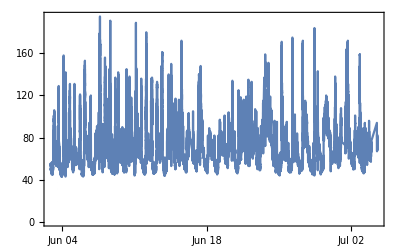

```mathematica
DateListPlot [ Take[Transpose[{dates, heartRatePoints}], -25000]]
```

```mathematica
SetDirectory[NotebookDirectory []]
```

/Users/jofre/Documents/GitHub/Connie_Summer2018

```mathematica
dates= Import[ "DateObject.mx"]
```

{Mon 6 Feb 2017 19:58:53GMT-4.,Mon 6 Feb 2017 20:03:21GMT-4.,Mon 6 Feb 2017 20:06:30GMT-4.,257622,Wed 4 Jul 2018 14:16:59GMT-4.,Wed 4 Jul 2018 14:22:11GMT-4.,Wed 4 Jul 2018 14:25:36GMT-4.}
 |  |  |  |

```mathematica
dateObjects= %131 ;
SetDirectory[NotebookDirectory []]
Export ["DateObject2.mx", dateObjects ,"MX" ]
```

DateObject::zone: Argument … in DateObject is not a recognized TimeZone specification.

/Users/jofre/Documents/GitHub/Connie_Summer2018

DateObject2.mx

## Import Saved Data

```mathematica
heartRatePoints = getAllHeartPoints [ Drop[heartRate,1]]
```

```mathematica
dobjs=Import["DateObject2.mx"];
```

```mathematica
DateListPlot [ Take[Transpose[{dobjs,heartRatePoints}],-25000]]
```

# Activity , resting HR

```mathematica
sleepData =getImportantData[Import["HKCategoryTypeIdentifierSleepAnalysis.csv","CSV"]];
```

```mathematica
sleepData//Length
```

3299

```mathematica
sleepData[[1]]
```

type;sourceName;sourceVersion;device;creationDate;startDate;endDate;value

```mathematica
sleepData[[14]]
```

HKCategoryTypeIdentifierSleepAnalysis;Pillow;089;;2017-02-08 03:50:25 -0400;2017-02-07 20:33:31 -0400;2017-02-07 21:21:16 -0400;HKCategoryValueSleepAnalysisAsleep

```mathematica
StringCases["HKCategoryValueSleepAnalysisAsleep",(_UpperCaseQ~~__LowerCaseQ)]
```

StringExpression::invld: Element _UpperCaseQ is not a valid string or pattern element in _UpperCaseQ~~__LowerCaseQ.

```mathematica
StringCases["HKCategoryValueSleepAnalysisAsleep",_?UpperCaseQ~~__?LowerCaseQ]
```

{Category,Value,Sleep,Analysis,Asleep}

```mathematica
{"HKCategoryValueSleepAnalysisDeepAsleep"}/."HKCategoryValueSleepAnalysisDeepAsleep"->"Deep Sleep"
```

{Deep Sleep}

```mathematica
getImportantData[ sleepData ];
```